Interstellar Ring
Ruth Gregory
Aldo Riello
Ifigeneia Giannakoudi

### 3. Null geodesics in a Schwarzschild’s spacetime

```mathematica
Rs= 2;
```

### (a) Define the effective potential Ueff[u , b ]. Plot Ueff[u, b] for b = 4, 3√3, 7 in the range −0.3 < u < 2. What do you notice? Cf. Eq. 6.3.33 of Wald.

```mathematica
(* Define Ueff[u,b] *)
Ueff[u_,b_]:=1/b^2 -u^2 +Rs* u^3
```

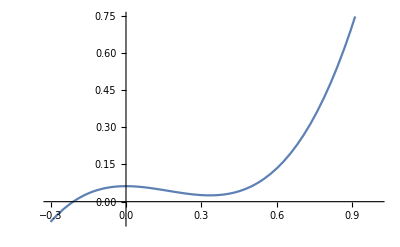

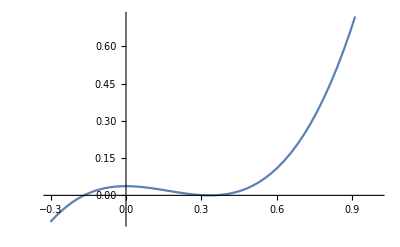

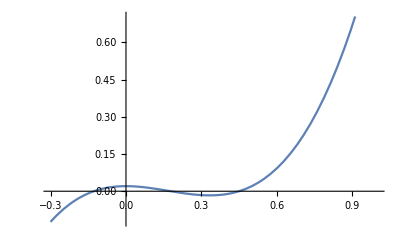

```mathematica
(* Plot Ueff[u,b] for b=4,3√3,7 in the range−0.3<u<2 (seperate plots)*)

p1 = Plot[Ueff[u, 4],{u,-0.3,1}]
p2 = Plot[Ueff[u, 3 √3],{u,-0.3,1}]
p3 = Plot[Ueff[u, 7],{u,-0.3,1}]
```

```mathematica
(* What do you notice? Define bmin *)
bmin = 3 √3 (* Any light reaching the observer must not be trapped by the black hole to start with *)

(* Following Wald, we expect that the smallest b for which the geodesic is not trapped by the black hole is b = 3√3 M = 3√3. In the plots above, the u = 0 points correspond to r = ∞ and there, the motion looks like free motion with impact parameter b. From the geodesic equation , we know that if  vanishes, the light geodesic's radial motion stops at the corresponding u ensuring the existence of a periastron for the motion which returns to infinity after reaching it. Such a zero ceases to exist for b < 3 √3 and the geodesic has u growing until it is absorbed by the black hole *)
```

4

### (c) Define r0[b]

```mathematica
(* solve the corresponding equation to find periastron *)
```

```mathematica
r01[b_]=(u/. Solve[1/b^2 -u^2 +Rs* u^3==0,u])[[1]]
r02[b_]=(u/. Solve[1/b^2 -u^2 +Rs* u^3==0,u])[[2]]
r03[b_]=(u/. Solve[1/b^2 -u^2 +Rs* u^3==0,u])[[3]]

(* The plots of  above show that there is a zero on the negative u axis. The two other possible zeros (elements 2 and 3) are both real beyond the critical b. We select the one with smalest positive u as the periastron *)
```

1/6 (1+1/((1-54/b^2+(6 √3 √(27-b^2))/b^2)^(1/3))+(1-54/b^2+(6 √3 √(27-b^2))/b^2)^(1/3))

1/6-(1+ⅈ √3)/(12 (1-54/b^2+(6 √3 √(27-b^2))/b^2)^(1/3))-1/12 (1-ⅈ √3) (1-54/b^2+(6 √3 √(27-b^2))/b^2)^(1/3)

1/6-(1-ⅈ √3)/(12 (1-54/b^2+(6 √3 √(27-b^2))/b^2)^(1/3))-1/12 (1+ⅈ √3) (1-54/b^2+(6 √3 √(27-b^2))/b^2)^(1/3)

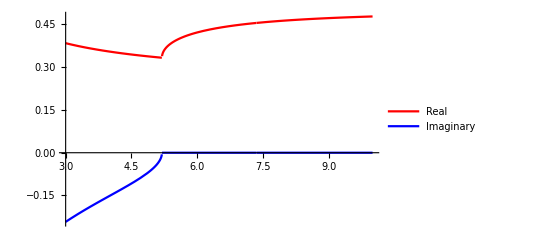

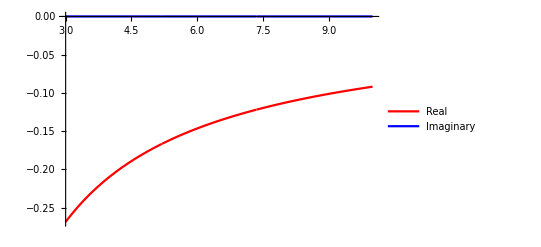

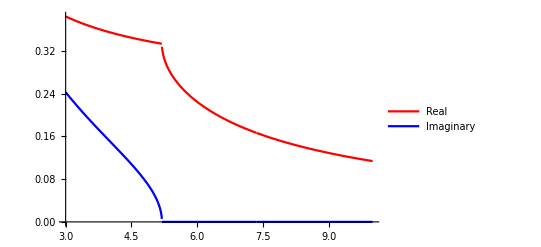

1/6-(1-ⅈ √3)/(12 (1-54/b^2+(6 √3 √(27-b^2))/b^2)^(1/3))-1/12 (1+ⅈ √3) (1-54/b^2+(6 √3 √(27-b^2))/b^2)^(1/3)

```mathematica
(* Plot here for b in (3,10) *)
p1 =ReImPlot[r01[b],{b,3,10}, PlotLegends->Automatic,ReImStyle->{Red,Directive[Blue,Dashing[{}]]},ReImLabels->{"Real","Imaginary"}] (* Furthest u zero moving to higher u as b increases *)
p2 =ReImPlot[r02[b],{b,3,10}, PlotLegends->Automatic,ReImStyle->{Red,Directive[Blue,Dashing[{}]]},ReImLabels->{"Real","Imaginary"}] (* Negative axis zero *)
p3 =ReImPlot[r03[b],{b,3,10}, PlotLegends->Automatic,ReImStyle->{Red,Directive[Blue,Dashing[{}]]},ReImLabels->{"Real","Imaginary"}] (* Periastron zero *)

r0[b_]=(u/. Solve[1/b^2 -u^2 +Rs* u^3==0,u])[[3]]
```

```mathematica
u0[b_]:= 1/Re[r0[b]]
```

### (d) Define the function bcrit[a]

```mathematica
bcrit[a_]:= 1/Sqrt[1/a^2 - Rs*1/a^3]
```

### (e) Do a Parametric plot of the shape of the geodesic on the plane χ = π/2; use the function psiofu[u , b ] and do the plot for the values b = 4, 3√3, 7. What do you notice for the trajectory associated to b = 3√3?

```mathematica
(* Integrate up to the periastron because then u changes sign*)
psiofu[u_,b_] := NIntegrate[1/Sqrt[Ueff[ui, b]], {ui, 0, u}]
```

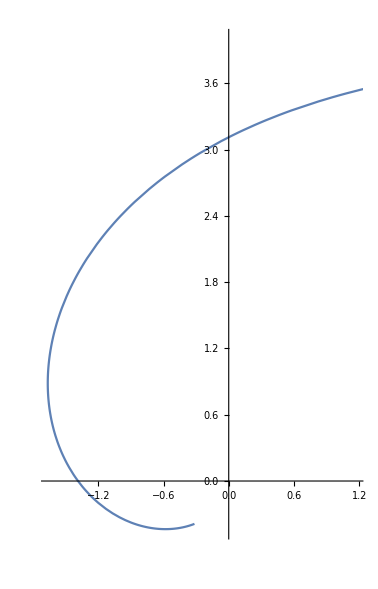

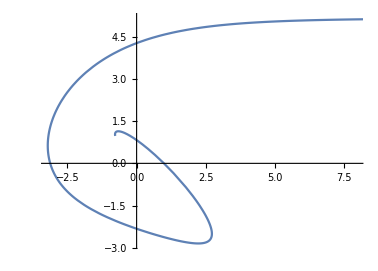

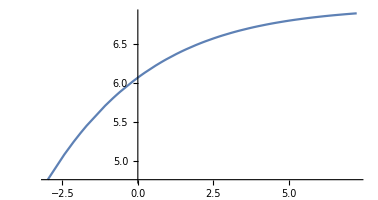

```mathematica
(* 3 Different Plots here *)

ParametricPlot[{1/u*Cos[psiofu[u,4]],1/u*Sin[psiofu[u,4]]},{u,0.01,2}]


ParametricPlot[{1/u*Cos[psiofu[u,3 √3-0.01]],1/u*Sin[psiofu[u,3√3-0.01]]},{u,0.01,1}]
(* We see that geodesics with b smaller than the critical value 3√3, there is no return to infinity after approaching the black hole (light is trapped). *)

ParametricPlot[{1/u*Cos[psiofu[u,7]],1/u*Sin[psiofu[u,7]]},{u,0.1,Re[u0[4]]}]
(* Thanks to Maitá for advising to use the Re[] function here *)
```

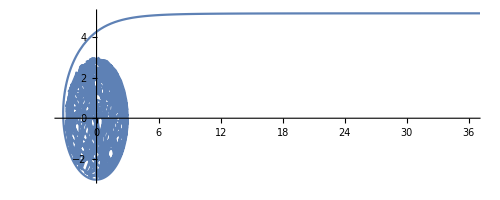

```mathematica
(* Parametric Plot for b = (3 √3 *)
ParametricPlot[{1/u*Cos[psiofu[u,3 √3]],1/u*Sin[psiofu[u,3 √3]]},{u,0.01,0.35}]
(* The critical geodesic is unstable and sensitive to numerical error *)
```

### (f) Define two functions Psi[b ,a ] and Psiplus[b ,a ] corresponding to the two branches of the partial deflection angle Δψ_ϕ as parametrized by the initial radial position and the final impact parameter of the geodesics labelled by φ. Fix a = 6 and plot these two branches in a unique graph where Y = Δψ_ϕ and X = b

```mathematica
Psi[b_,a_]:= NIntegrate[1/Sqrt[Ueff[ui, b]], {ui, 0, 1/a}]
```

```mathematica
Psiplus[b_,a_]:= 2*NIntegrate[1/Sqrt[Ueff[ui, b]], {ui, 0,ComplexExpand[ Re[u0[b]]]}]-Psi[b,a]
```

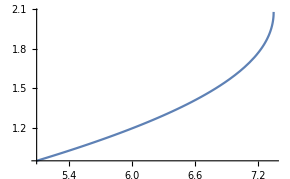

```mathematica
(* Plot together for a=6 *)
p1 = Plot[Psi[b,6],{b,3 √3-0.1,bcrit[6]}];
p2 = Plot[Psiplus[b,6],{b,3 √3-0.1, bcrit[6]}];
Show[p1, p2]
```

```mathematica
NIntegrate[1/Sqrt[Ueff[ui, b]], {ui, 0, ComplexExpand[Re[u0[b]]]}]
```

NIntegrate::nlim: ui = 1/(0.166667-(0.0833333 Cos[«1»])/(((«1»)^2+«1»)^(1/6))-«20» «1» («1»)^(«1»)+(«20» «1»)/(«1»)+0.144338 ((1.+«1»+Times[«4»])^2+(108. «1»«1»«1»)/b^4)^(1/6) Sin[0.333333 Arg[1.+Times[«2»]+Times[«3»]]]) is not a valid limit of integration.

```mathematica
NIntegrate[1/(√Ueff[ui,b]),{ui,0,ComplexExpand[Re[u0[6]]]}]
```

NIntegrate::inumr: The integrand 1/(√(1/b^2-ui^2+2 ui^3)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4.45336}}.

NIntegrate[1/(√Ueff[ui,b]),{ui,0,ComplexExpand[Re[u0[6]]]}]

```mathematica
ComplexExpand[Re[u0[5]]]
```

1/(1/6+1/(12 (29/25-(6 √6)/25)^(1/3))+1/12 (29/25-(6 √6)/25)^(1/3))

### 4. Observer’s frame

```mathematica
Theta[phi_,theta0_] :=
```

```mathematica
(* Plot for theta0=π/3 *)
```

### 5. Drawing the observed disk

```mathematica
(* Plot for Psi and Psiplus again for a = 6 *)
```

```mathematica
(* find and set the value of the impact parameter where the branches seperate*)
bamax =
```

We will reverse the function ψ(b) numerically. So, we will work with the 2 branches separately.

```mathematica
(* We set a discrete grid of values for Psi[b,6] for values of b from bmin to bmax with a step of 0.01 for the first branch. The values of Psi are saved in the first line and the corresponding b values in the second line. We will do the same for the second branch and then we can 'reverse' the function in the sense that we know the Psi's corresponding to b's but the table can also give the b's corresponding to Psi's, which is single valued. *)
psi1 = Table[{Psi[b,6],b},{b,bmin, bmax, 0.01}];
```

```mathematica
(* We set a deiscrete grid of values for Psi[b,6] for values of b from bmin+0.2 (for numerical reasons) to bmax with a step of 0.01 for the second branch, and then reverse the table because the function is descending *)
psi2 = Reverse[Table[{Re[Psiplus[b,6]],b},{b,bmin+0.006, bmax, 0.01}]];
```

```mathematica
(* We join the two branches, so with these points we could recreate Psi[b,6]*)
fullpsi = Join[psi1,psi2];
```

```mathematica
(* We join the two branches, so with these points we could recreate Psi[b,6]*)
x = fullpsi[[All,2]];
y = fullpsi[[All,1]]/Pi;
ListPlot[Transpose[{x,y}],PlotRange-> {0,3}]
```

If everything is going well, this plot should resemble the initial analytic plot in the beginning of this section.

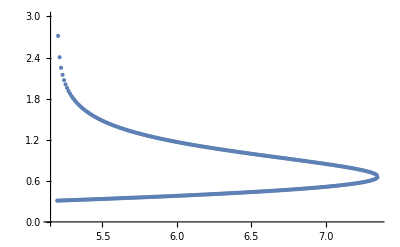

```mathematica
(* We use interpolation now to find b(Psi), essentially we use the pairs (Psi,b) of the fullpsi table and we interpolate the analytic form of the function. We end up with the desired b(Psi).*)
bofpsi = Interpolation[fullpsi] (* this works like a function *)
bofpsi[Pi] (* the result should be around 6.48*)
```

InterpolatingFunction[…]

6.4816

```mathematica
(* We found b(Psi), but we want b(phi). We know that Psi[b,6]= Theta[phi,theta0], so to find b[phi], we will find the b[Theta[phi,theta0]]*)
Impact[phi_,theta0_]:=
```

```mathematica
(* Plot Impact for theta0=Pi/3 *)
```

```mathematica
(* Use ParametricPlot to plot the rings for theta0=Pi/3 , 0.4Pi and 0.45 Pi *)
```